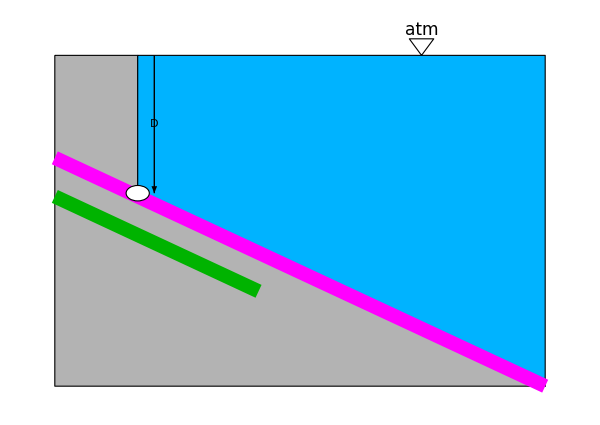

```mathematica
Module[{θ,d,h,L0,w},
θ=35°;d=1.25;h=3;L0=0.5;w=3*Cos[θ];

Graphics[{EdgeForm@Thick,
{FaceForm@GrayLevel@0.7,Polygon[{{0,h},{L0,h},{L0,h-d},{L0+w,0},{0,0}}]},
{FaceForm@RGBColor[0,0.7,1],Polygon[{{L0,h},{L0+w,h},{L0+w,0},{L0,h-d}}]},
{FaceForm@None,Polygon[{{0.9*w,h},{0.87*w,1.05*h},{0.93*w,1.05*h}}]},
{Thick,Arrowheads@{-Large,Large},Arrow[{{1.2*L0,h},{1.2*L0,h-d}}]},
Text[Framed[Style["D",18,Italic],Background->RGBColor[0,0.7,1],FrameStyle->None,FrameMargins->Tiny],{1.2*L0,h-d/2}],
Text[Style["atm",17],{0.9*w,1.05*h},{0,-1}],
(*{Thickness@0.017,CapForm@"Round",
Magenta,Line[{{L0+w,0},{0,(L0+w)*Tan[θ]}}],
RGBColor[0,0.7,0],Line[{{1.5*Cos[θ],1.5*Sin[θ]},{0,1.5*Sin[θ]+1.5*Cos[θ]*Tan[θ]}}]},*)
{Thickness@0.017,CapForm@"Round",
Magenta,Line[{{L0+w,0},{0,(L0+w)*Tan[θ]}}],
RGBColor[0,0.7,0],Line[{{#*Cos[θ],#*Sin[θ]},{0,#*Sin[θ]+#*Cos[θ]*Tan[θ]}}]&@1.5},
{FaceForm@White,Disk[{L0,h-d},0.07]},
},ImageSize->{600,425}]
]
```

```mathematica
{2.44,0}
```

```mathematica
N@3*Cos[35°]
```

2.45746

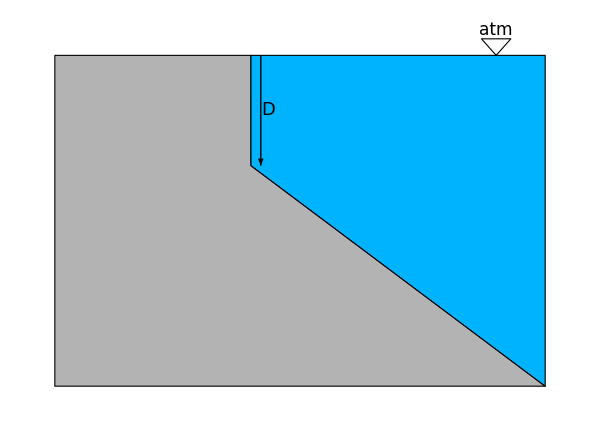

```mathematica
Module[{H1,H2,L1,L2},
H1=1;H2=3;L1=2;L2=5;

Graphics[{
{EdgeForm@Thick,FaceForm@GrayLevel@0.7,Polygon[{{0,H2},{L1,H2},{L1,H2-H1},{L2,0},{0,0}}]},
{EdgeForm@Thick,FaceForm@RGBColor[0,0.7,1],Polygon[{{L1,H2},{L2,H2},{L2,0},{L1,H2-H1}}]},
{EdgeForm@Thick,FaceForm@None,Polygon[{{0.9*L2,H2},{0.87*L2,1.05*H2},{0.93*L2,1.05*H2}}]},
Thick,Arrowheads@{-Large,Large},Arrow[{{1.05*L1,H2},{1.05*L1,H2-H1}}],(*Arrow[{{0.115*L1,H2},{L1+0.35*L2,0.2*H2}}],*)
Text[Style["D",18,Italic],{1.05*L1,H2-H1/2},{-2,0}],
Text[Style["atm",17],{0.9*L2,1.05*H2},{0,-1}]
},ImageSize->{600,425}]
]
```

```mathematica
N@1/12
```

0.0833333

```mathematica
9800*(1.25+1.5*Sin[35°])*3*2.5
```

155112.

```mathematica
Module[{w,h,d,z,θ,yc,A,Ixc},
w=2.5;h=3;d=1.25;z=1.5;(*m*)
θ=35°;yc=z+d/Sin[θ];
A=w*h;
Ixc=1/12*w*h^3;

yc+Ixc/(yc*A)
]
```

3.88315